# Anharmonic Chains

Reference: Herbert Spohn, Nonlinear fluctuating hydrodynamics for anharmonic chains. J. Stat. Phys. 154, 1191-1227 (2014), arXiv:1305.6412

Square-well potential with alternating masses at zero pressure p

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<"anharm_chains_max_dist.m";
```

## Import initial data

```mathematica
(* load position data from disk *)
Subscript[r, data,0]=Import["collision_test2_field_r0.dat","Real64"]
Length[%]
```

{0.127913,0.166067,0.0621915,0.770192,0.872599,0.127694,0.882688,0.971164,0.888497,0.741524,0.181617,0.246662,0.750785,0.793615,0.879285,0.115535}

16

```mathematica
(* average elongation, should be conserved *)
Mean[Subscript[r, data,0]]
```

0.536127

```mathematica
Subscript[q, data,0]=Most[Accumulate[Prepend[Subscript[r, data,0],0]]]
Length[%]
```

{0,0.127913,0.29398,0.356171,1.12636,1.99896,2.12666,3.00934,3.98051,4.86901,5.61053,5.79215,6.03881,6.78959,7.58321,8.46249}

16

```mathematica
(* load momentum data from disk *)
Subscript[p, data,0]=Import["collision_test2_field_p0.dat","Real64"]
```

{0.695259,-1.49671,0.404693,-1.0769,0.668085,-2.80978,0.338052,-0.0189182,-0.300148,2.70245,-1.26843,3.56142,0.406422,1.56139,-1.12714,2.3231}

```mathematica
(* expectation value is zero, but not current actual value *)
Mean[Subscript[p, data,0]]
```

0.285178

```mathematica
(* alternating masses *)
Subscript[m, 0,1,val]={1,3};
```

```mathematica
Subscript[mass, val]=Flatten[ConstantArray[Subscript[m, 0,1,val],Length[Subscript[q, data,0]]/2]]
```

{1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3}

```mathematica
(* square-well potential width *)
Subscript[a, val]=1;
```

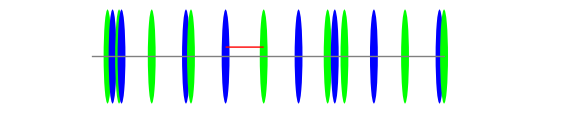

```mathematica
VisualizeField[Accumulate[Prepend[Subscript[r, data,0],0.4]],Append[Subscript[mass, val],First[Subscript[mass, val]]]/Mean[Subscript[m, 0,1,val]],Subscript[a, val],9]
```

```mathematica
(* without taking collisions into account *)
Animate[VisualizeField[Subscript[q, data,0]+0.4+t Subscript[p, data,0]/Subscript[mass, val],Append[Subscript[mass, val],First[Subscript[mass, val]]]/Mean[Subscript[m, 0,1,val]],Subscript[a, val],9],{t,0,10},AnimationRunning->False]
```

## Run simulation

```mathematica
(* example *)
NextCollision[Subscript[r, data,0],Subscript[p, data,0],Subscript[mass, val],Subscript[a, val]]
```

{2.85226,0.0634839,CollString,15}

```mathematica
(* example *)
UpdateField[{Subscript[q, data,0],Subscript[p, data,0],0},Total[Subscript[r, data,0]],Subscript[mass, val],Subscript[a, val]];
Differences[First[%]]
```

{0.052103,0.223431,0.0137114,0.835393,0.770728,0.208614,0.860827,0.952509,0.964739,0.603812,0.337506,0.197099,0.758025,0.689019,1.}

```mathematica
Subscript[f, seq]=FieldSequence[{Subscript[q, data,0],Subscript[p, data,0],0},Total[Subscript[r, data,0]],Subscript[mass, val],Subscript[a, val],79];
Length[%]
```

80

```mathematica
(* example *)
Subscript[f, seq]⟦{1,2,-1}⟧
```

{{{0,0.127913,0.29398,0.356171,1.12636,1.99896,2.12666,3.00934,3.98051,4.86901,5.61053,5.79215,6.03881,6.78959,7.58321,8.46249},{0.695259,-1.49671,0.404693,-1.0769,0.668085,-2.80978,0.338052,-0.0189182,-0.300148,2.70245,-1.26843,3.56142,0.406422,1.56139,-1.12714,2.3231},0},{{0.0441378,0.0962407,0.319671,0.333383,1.16878,1.9395,2.14812,3.00894,3.96145,4.92619,5.53,5.86751,6.06461,6.82264,7.51165,8.51165},{0.695259,-1.49671,0.404693,-1.0769,0.668085,-2.80978,0.338052,-0.0189182,-0.300148,2.70245,-1.26843,3.56142,0.406422,1.56139,1.72512,-0.529157},0.0634839},{{0.130748,0.672593,1.67259,2.13243,2.38412,3.25862,4.00443,4.1795,4.41652,5.35888,5.74587,6.23889,6.74559,7.14485,7.57263,7.98938},{0.685874,2.68531,-0.420421,0.329557,-0.31066,-1.85694,-1.27232,1.03613,0.599426,2.09843,-1.25952,-2.05903,-0.631667,3.42438,1.38999,0.124319},4.95764}}

```mathematica
Interpolation[{Last[#],First[#]}&/@Subscript[f, seq],InterpolationOrder->1]
Animate[VisualizeField[%[t],Subscript[mass, val]/Mean[Subscript[m, 0,1,val]],Subscript[a, val],9],{t,0,3},AnimationRunning->False]
```

InterpolatingFunction[{{0., 4.95764}}, <>]

## Compare with C implementation

```mathematica
CollisionInfo[{q_List,p_List,t_},L_,mass_,a_]:=Module[{r=FieldDifferences[q,L],Δt,type,i},
	{Δt,type,i}=Rest[NextCollision[r,p,mass,a]];{t+Δt,type,i}]
```

```mathematica
(* reference *)
Subscript[coll, ref]=CollisionInfo[AdvanceField[#,Subscript[mass, val],0.0001],Total[Subscript[r, data,0]],Subscript[mass, val],Subscript[a, val]]&/@Subscript[f, seq];
Length[%]
```

80

```mathematica
(* example *)
Subscript[coll, ref]⟦{1,2,-1}⟧
```

{{0.0634839,CollString,15},{0.0814387,CollCore,3},{5.15518,CollCore,10}}

```mathematica
(* load C implementation results from disk *)
"collision_test2_event_";
Subscript[coll, test]=Transpose[{(* event times *)Import[%<>"time.dat","Real64"],(* event types *) Import[%<>"type.dat","Integer32"]/.{0->CollString,1->CollCore},(* particle indices *)Import[%<>"iprt.dat","Integer32"]+1}];
Length[%]
```

80

```mathematica
(* example *)
Subscript[coll, test]⟦{1,2,-1}⟧
```

{{0.0634839,CollString,15},{0.0814387,CollCore,3},{5.15518,CollCore,10}}

```mathematica
(* compare *)
Norm[Subscript[coll, ref]-Subscript[coll, test]]
```

9.16304×10^-14

```mathematica
(* save reference to disk for comparison *)
"collision_test2_ref_event_";
{(* event times *)Export[%<>"time.dat",Subscript[coll, ref]⟦;;,1⟧,"Real64"],(* event types *) Export[%<>"type.dat",Subscript[coll, ref]⟦;;,2⟧/.{CollString->0,CollCore->1},"Integer32"],(* particle indices *)Export[%<>"iprt.dat",Subscript[coll, ref]⟦;;,3⟧-1,"Integer32"]};
```